```mathematica
(*I^2 / V*)
(*Import and organize data*)

dtset = Import["/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/9_Lab/table.csv"];
```

Wavelength (nm) | Inverse | Predicted | Residuals
388.906 | 4.20779 | 4.26852 | -0.0607285
397.008 | 4.26667 | 4.30199 | -0.0353169
410.173 | 4.35556 | 4.35638 | -0.000819876
434.047 | 4.5 | 4.45501 | 0.0449891
486.135 | 4.7619 | 4.6702 | 0.0916962
656.279 | 5.33333 | 5.37313 | -0.0397982

2.66104+0.00413016 x

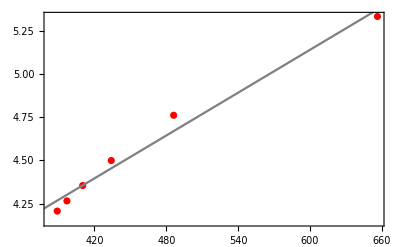
-Graphics-inverse of wavelength (1/nm)inverse of (1/n₂.b2 - 1/n₁.b2)

```mathematica
col1 = dtset[[All, 1]][[2 ;; 7]]; (*inverse*)
 col2 = dtset[[All, 2]][[2 ;; 7]];(*wavelength)*)

(*Display table*)
TableForm[dtset]

(*Pair Data*)
col3 = col2 / 1.00029;
dataInterpolate2 = {col1, col3};
dataBund2 = Transpose[dataInterpolate2];

(*Graph Data*)
ListPlot[dataBund2,PlotMarkers->{"o",Large}];

(*Least Squares Fit*)
lm = LinearModelFit[dataBund2, x, x];
Normal@lm  (*Print out line of least squares fit*)

s2= Labeled[
Show[
ListPlot[dataBund2, PlotStyle->Red],
Plot[lm[x],{x,0,1000}, PlotStyle->Gray], (*Take note of bounds*)
Frame->True], 
{"inverse of wavelength (1/nm)", "inverse of (1/n₂.b2 - 1/n₁.b2)"},
{Bottom, Left},
RotateLabel->True
]
```

```mathematica
r =0.0021184619167450547;
g = 9.109383 * 10^(-31);
h = 1.675326 * 10^(-27);
r* (1 + g/h)
```

```mathematica
0.0021196138048534315 * 10000000
```

21196.1

```mathematica
(*Residual Plot*)
```

```mathematica
col3= dtset[[All, 2]][[2 ;; 7]];(*predicted*)
col4 = dtset[[All, 2]][[2 ;; 7]]; (*residuals*)
col5 = {0.2, 0.2, 0.2, 0.2, 0.2, 0.2};
lab9PlotPairErrs = {col1, col4};
lab9PlotPairErrsTuple = Transpose[lab9PlotPairErrs];
lab9PlotPairErrsWU = {col1, col4, col5};
lab9PlotPairErrsWUTuple = Transpose[lab9PlotPairErrsWU];
```

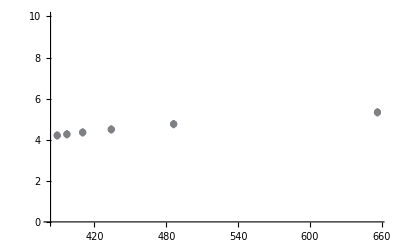
-Graphics-inverse of wavelength (1/nm)inverse of (1/n₂.b2 - 1/n₁.b2) residuals

```mathematica
Needs["ErrorBarPlots`"]
l2 = Labeled[
	Show[
	ListPlot[lab9PlotPairErrsTuple, PlotRange->{0, 10}],     (*Note the Range*)
	Plot[lm[x],{x,0,12}],
	ErrorListPlot[lab9PlotPairErrsWUTuple,PlotStyle->Gray]
   ],
{"inverse of wavelength (1/nm)", "inverse of (1/n₂.b2 - 1/n₁.b2) residuals"},
{Bottom, Left},
RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"graph_residual9.png", l2, ImageResolution-> 200]
Export[NotebookDirectory[]<>"graph9.png", s2, ImageResolution-> 200]
```

/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/9_Lab/graph_residual9.png

/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/9_Lab/graph9.png